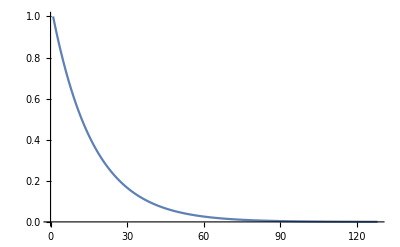

```mathematica
sr=128;ts=1/sr;
d=Table[0,{x,0,sr-1}];d[[1]]=1;
p=0.94;
Do[d[[i]]=p d[[i-1]]+d[[i]],{i,2,Length@d}];
ListLinePlot[d,PlotRange->Full]
```

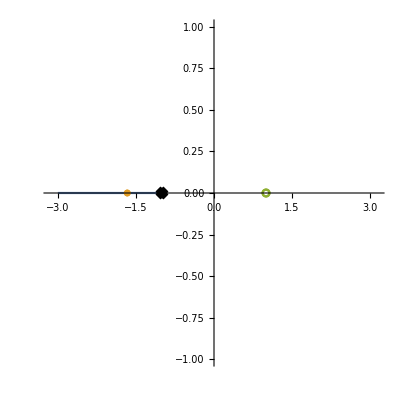

```mathematica
RootLocusPlot[TransferFunctionModel[1/(1+q((1-z)/(1+z))),z],{q,0,1},PlotRange->{{-Pi,Pi},{-1,1}},AspectRatio->1]
```

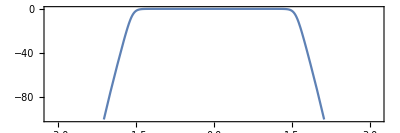

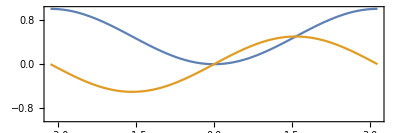

```mathematica
q=1;
o=1;
lp[f_,o_]:=1/(1+q(((E^(I f)-1)/(E^(I f)+1))((E^(-I f)-1)/(E^(-I f)+1)))^o);
hp[f_]:=1/(1+q(E^(I f)+1)/(E^(I f)-1));
dB[x_]:=20Log10[x]//N;
p1=Plot[dB@lp[f,10],{f,-Pi,Pi},PlotRange->{{-Pi,Pi},{-100,0}},Frame->True,PlotLegends->"Expressions",AspectRatio->1/3,WorkingPrecision->MachinePrecision]
p2=Plot[{Re@hp[f],Im@hp[f]},{f,-Pi,Pi},PlotRange->{{-Pi,Pi},{-1,1}},Frame->True,PlotLegends->"Expressions",AspectRatio->1/3]
```

```mathematica
Plot3D[Re[lp[f,2]//N],{f,-Pi,Pi},{q,-1,1}]
```

-Graphics3D-

```mathematica
p=.7;
Animate[
Plot[0,{x,0,1},
PlotRange->{{-1.2,1.2},{-1.2,1.2}},
AspectRatio->1,
Epilog->{Circle[{0,0}],
{Red,Line[{{0,0},{Cos@p,Sin@p}}]},
{Thick,Green,Line[{{0,0},{Cos@p,0}}]},
{Thick,Blue,Line[{{Cos@p,0},{Cos@p,Sin@p}}]},
{PointSize->Large,Point[{Cos@p,Sin@p}]}
}],{p,0,2Pi}]
```

```mathematica
Export["/tmp/anim.avi",%]
```

/tmp/anim.avi

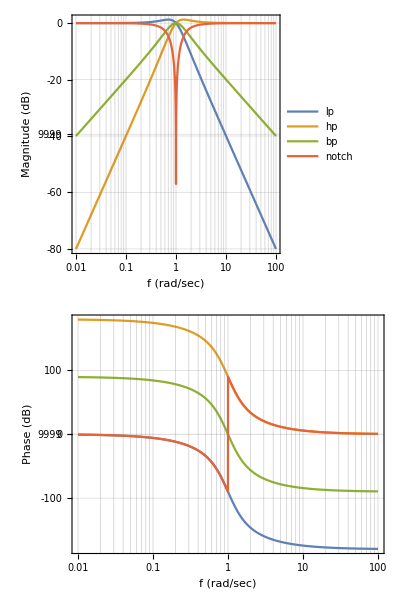

```mathematica
Module[{lp,hp,bp,notch},lp[q_]:=TransferFunctionModel[1/(s^2+s/q+1),s];
hp[q_]:=TransferFunctionModel[s^2/(s^2+s/q+1),s];
bp[q_]:=TransferFunctionModel[s/(s^2+s/q+1),s];
notch[q_]:=TransferFunctionModel[(s^2+1)/(s^2+s/q+1),s];
BodePlot[{lp[1],hp[1],bp[1],notch[1]},{0.01,100},ImageSize->Large,PlotLegends->{"lp","hp","bp","notch"},FrameLabel->{{"f (rad/sec)","Magnitude (dB)"},{"f (rad/sec)","Phase (dB)"}},GridLines->Automatic,AspectRatio-> 1/3]]
```

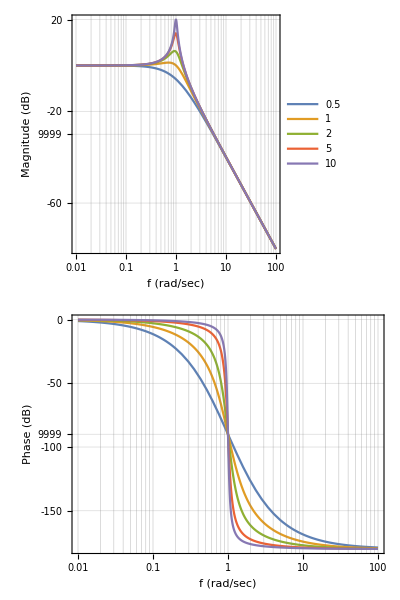

```mathematica
Module[{lp},lp[q_]:=TransferFunctionModel[1/(s^2+s/q+1),s];
qs={.5,1,2,5,10};
fs=Table[lp[q],{q,qs}];
BodePlot[fs,{0.01,100},ImageSize->Large,PlotLegends->{.5,1,2,5,10},FrameLabel->{{"f (rad/sec)","Magnitude (dB)"},{"f (rad/sec)","Phase (dB)"}},GridLines->Automatic,AspectRatio-> 1/3]]
```

```mathematica
σ=0;
(* https://www.youtube.com/watch?v=OXhW-h8Tkao *)
Manipulate[
NyquistPlot[TransferFunctionModel[(1+s)/(1-s),s],{-max,max},ImageSize->Large,AspectRatio->1,PlotRange->{{-1,1},{-1,1}}],{{max,0.002},0.002,10}
]
```